```mathematica
Integrate[Exp[-p^2/2/m/k/T],{p,-Infinity,Infinity}]//FullSimplify
```

ConditionalExpression[(√(2 π))/(√(1/(k m T))),Re[1/(k m T)]>0]

```mathematica
Integrate[Exp[q E0 x/k/T],{x,0,L/2}]
```

((-1+ⅇ^((E0 L q)/(2 k T))) k T)/(E0 q)

```mathematica
Integrate[Exp[-q E0 x/k/T],{x,L/2,L}]
```

(ⅇ^(-(E0 L q)/(k T)) (-1+ⅇ^((E0 L q)/(2 k T))) k T)/(E0 q)

4.85797×10^6

{2.81731322785376×10^8,2.68314982691354×10^8,2.56118309878607×10^8,2.44982217310446×10^8,2.34774132456299×10^8,2.25382694390483×10^8,2.16713674637423×10^8,2.086868044957×10^8,2.01233282221243×10^8,1.94293795965715×10^8,1.87816942127221×10^8}

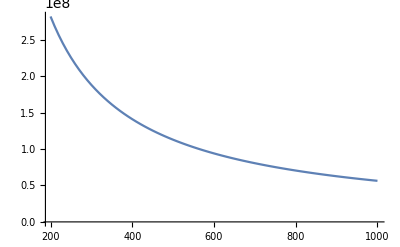

```mathematica
Block[
{n=2000,q=1.6*10^(-19),E0=10^15,a=4.19*10^(-10),kB=1.38*10^(-23),T},
Print[(q E0 a/2/kB/T)/.{T->500}];
Print[Table[Log[n^(2/3)/Gamma[n/2+1]^2 (Cosh[q E0 a/2/kB/T(2n^(1/3)-1)]-Cosh[q E0 a/2/kB/T])/Sinh[q E0 a/2/kB/T]],{T,200,300,10}]];
Print[ListLinePlot[Table[{T,Log[n^(2/3)/Gamma[n/2+1]^2 (Cosh[q E0 a/2/kB/T(2n^(1/3)-1)]-Cosh[q E0 a/2/kB/T])/Sinh[q E0 a/2/kB/T]]},{T,200,1000,10}]]];
]
```

4.85797×10^6

{2.81731322785376×10^8,2.68314982691354×10^8,2.56118309878607×10^8,2.44982217310446×10^8,2.34774132456299×10^8,2.25382694390483×10^8,2.16713674637423×10^8,2.086868044957×10^8,2.01233282221243×10^8,1.94293795965715×10^8,1.87816942127221×10^8}

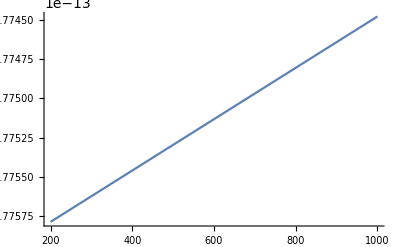

```mathematica
Block[
{n=2000,q=1.6*10^(-19),E0=10^15,a=4.19*10^(-10),kB=1.38*10^(-23),T},
Print[(q E0 a/2/kB/T)/.{T->500}];
Print[Table[Log[n^(2/3)/Gamma[n/2+1]^2 (Cosh[q E0 a/2/kB/T(2n^(1/3)-1)]-Cosh[q E0 a/2/kB/T])/Sinh[q E0 a/2/kB/T]],{T,200,300,10}]];
Print[ListLinePlot[Table[{T,-kB T Log[n^(2/3)/Gamma[n/2+1]^2 (Cosh[q E0 a/2/kB/T(2n^(1/3)-1)]-Cosh[q E0 a/2/kB/T])/Sinh[q E0 a/2/kB/T]]},{T,200,1000,10}]]];
]
```

4.85797×10^6

{8.7009972046468×10^8,8.28644670142241×10^8,7.90958260758207×10^8,7.56548930451045×10^8,7.25007044336146×10^8,6.95988509110439×10^8,6.69202168902095×10^8,6.44400002042516×10^8,6.21369418530051×10^8,5.99927151121893×10^8,5.79914368207612×10^8}

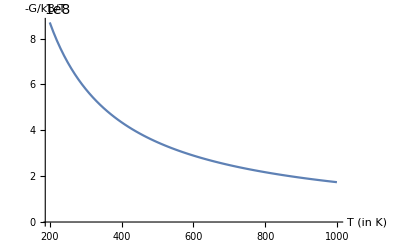

```mathematica
Block[
{n=5*10^4,q=1.6*10^(-19),E0=10^15,a=4.19*10^(-10),kB=1.38*10^(-23),T},
Print[(q E0 a/2/kB/T)/.{T->500}];
Print[Table[Log[n^(2/3)/Gamma[n/2+1]^2 (Cosh[q E0 a/2/kB/T(2n^(1/3)-1)]-Cosh[q E0 a/2/kB/T])/Sinh[q E0 a/2/kB/T]],{T,200,300,10}]];
Print[ListLinePlot[Table[{T,Log[n^(2/3)/Gamma[n/2+1]^2 (Cosh[q E0 a/2/kB/T(2n^(1/3)-1)]-Cosh[q E0 a/2/kB/T])/Sinh[q E0 a/2/kB/T]]},{T,200,1000,10}],AxesLabel->{"T (in K)","-G/kB/T"}]];
]
```